```mathematica
Quit
```

### 路线变分

```mathematica
Quit
```

```mathematica
δa1=0.5;
δa2=1.0;
y0=-2Sin[x]+x+1.5;
yp=k x+b;

sim={k->1/2,b->-1/2};
dy=Cos[yp π/.sim];
y1=y0+δa1 dy;
y2=y0+δa2 dy;
Plot[{y0,y1,y2},{x,2,8},PlotStyle->{Black,{Red,Dashing[{0.03,0.01}]},{Blue,DotDashed}},PlotRange->{{1.5,8.5},{0,10}}(*,Axes->False*),Ticks->None]
```

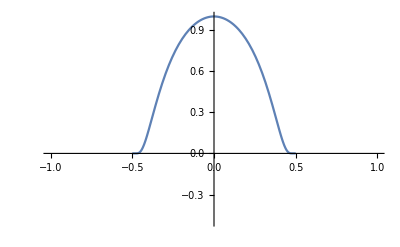

```mathematica
eps=0.5;
Plot[Exp[-1/(eps^2/x^2-1)],{x,-eps,eps},PlotRange->{{-1,1},{-0.5,1}}]
```

### 虚位移和实位移

```mathematica
x1=0.5;
y1=1;
Plot[{Sin[x]+x/2,y1+Sin[x+x1]+(x+x1)/2},{x,0,6},PlotStyle->{Black,{Dashed,Darker@Yellow}},Axes->False]
```

```mathematica
ParametricPlot[{θ-Sin[θ],-(1-Cos[θ])},{θ,0,1.2π},Axes->False,PlotRange->{{-.50,1.7π},{-2.5,0.5}}]
```

### 摆线

-Graphics-

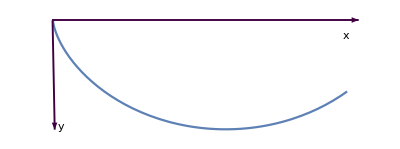

### 圆环

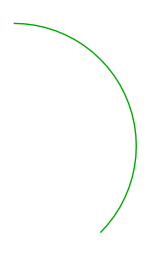

```mathematica
Graphics[{Darker@Green,Thick,Circle[{0,0},.2,{-45Degree,90Degree}]},ImageSize->150,PlotRange->1.5]
```

```mathematica
Graphics[{(*Darker@Green,*)Thick,Circle[{0,0},1,{π/4,π/2}]},ImageSize->150,PlotRange->{{-.50,1.7π},{-2.5,0.5}}]
```

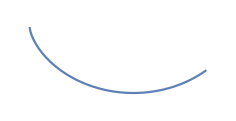

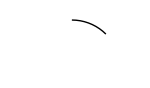

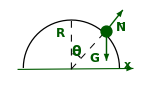

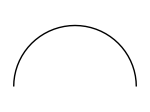
```mathematica
-Graphics--Graphics-
```

```mathematica
Plot[2Sin[x],{x,0,20π},AspectRatio->1.5/1,PlotStyle->Red]
```

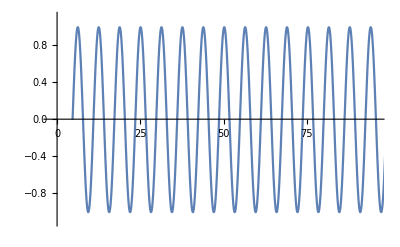

### Ex 3.3 图

```mathematica
Plot[{√-x,-√-x},{x,-1,0},PlotStyle->{Blue,Blue}]
```

-Graphics-

-Graphics-